# BloodVar effect on temperature rise (141126)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{140917-01-200um-2,5mW,500ms,0'2Hz,40T(Blood vessel).mat,140917-02-200um-2,5mW,500ms,0'2Hz,40T(No Blood vessel).mat,140917-03-200um-5mW,500ms,0'2Hz,40T(No Blood vessel).mat,140917-04-100um-5mW,500ms,0'2Hz,40T(No Blood vessel).mat,140917-05-400um-5mW,500ms,0'2Hz,40T(Half Blood vessel).mat,140917-06-200um-2,5mW,10000ms,0'05Hz,20T.mat}

## 2.5 mW 500 ms 450nm

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];
```

```mathematica
meanPlot[data_, color_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thick},PlotRange->All]
]


];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
trialPointLogPlot[data_, color_]:=Module[{},
ListLogPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {LightBlue,Blue,Darker[Blue],Purple,Pink,Red,Orange,Yellow,LightGreen,Green, Darker[Green]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gagColors=Table[ColorData["GrayTones",1-n],{n,0.2,1,0.8/1}]
```

{-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataBloodVar=Map[Import,gagFiles];
Dimensions/@gagFitDataBloodVar
```

{{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,20,2540}}

```mathematica
gagFitDataBloodVar= gagFitDataBloodVar[[{1,2}]];
Dimensions[gagFitDataBloodVar]
```

{2,1,40,620}

```mathematica
gagFitDataBloodVar=Flatten[gagFitDataBloodVar,1];
Dimensions/@gagFitDataBloodVar
```

{{40,620},{40,620}}

### Remove bad trials if necessary

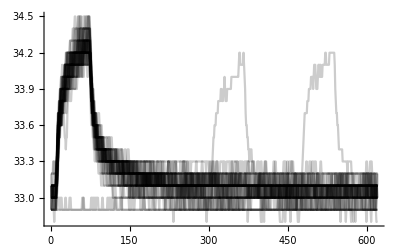
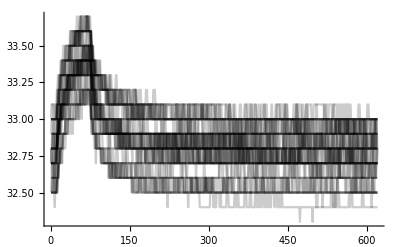

```mathematica
ListLinePlot[#,PlotStyle->Opacity[0.2,Black],PlotRange->All]&/@gagFitDataBloodVar
```

```mathematica
gagTemp=ListLinePlot[gagFitDataBloodVar[[1]],PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

-Graphics-

```mathematica
Ordering[gagFitDataBloodVar[[1]][[;;, 1]],1]
```

{24}

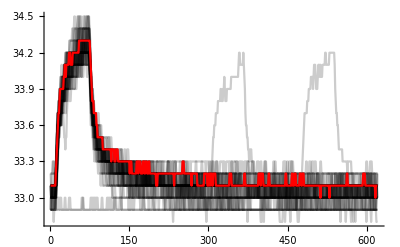

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataBloodVar[[1]][[11]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
gagFitDataBloodVar[[1]]=Delete [gagFitDataBloodVar[[1]],{{32},{39},{40}}];
Dimensions[gagFitDataBloodVar[[1]]]
```

{37,620}

```mathematica
Dimensions/@gagFitDataBloodVar
```

{{37,620},{40,620}}

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions/@gagFitDataBloodVar
```

{{37,620},{40,620}}

```mathematica
gagFitDataBloodVar=baselineNormalize/@ gagFitDataBloodVar;
```

```mathematica
Dimensions/@gagFitDataBloodVar
```

{{37,620},{40,620}}

```mathematica
501/(1000/128.) (*figuring out stim duration*)
```

64.128

```mathematica
stimDuration=64;
stimStart=11;
stimEnd=stimStart+stimDuration-4;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataBloodVar[[1, 1]]]
```

620

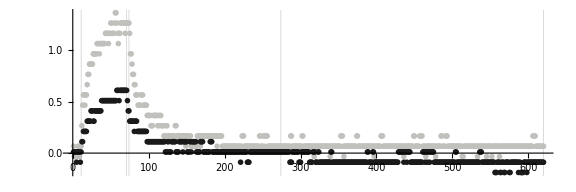

```mathematica
gagTempFitDataBloodVar=ListPlot[gagFitDataBloodVar[[All,1]],
GridLines->{{stimStart,stimEnd,fallStart,fallEnd,trialLength},None}, 
AspectRatio->1/3, ImageSize->72*8,PlotStyle->gagColors,PlotRange->All]
```

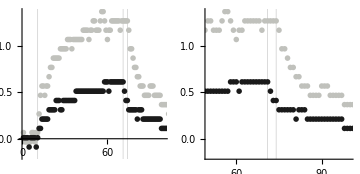

```mathematica
GraphicsRow[
{Show[gagTempFitDataBloodVar,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataBloodVar,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataBloodVar,gagColors}]]
```

{2,2}

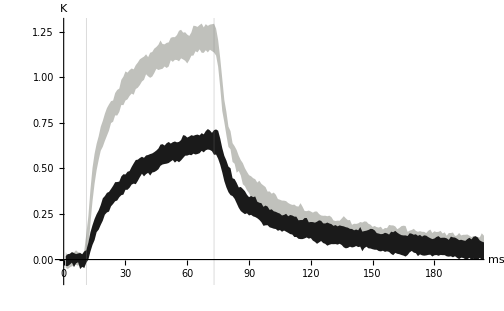

```mathematica
grSDBloodVar=Show[meanBandPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataBloodVar,gagColors}],
GridLines->{{stimStart,stimEnd+2},None}, PlotRange->{{0,200},All},AspectRatio->1/GoldenRatio,ImageSize->72*7, AxesLabel->{"ms", "K"},Ticks->{Automatic,Automatic}, 
AxesStyle->Thickness[0.0025], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0,0}]
```

```mathematica
legend={"Blood Vessel","No Blood Vessel"};
```

```mathematica
gagLegend=SwatchLegend[gagColors,legend,LabelStyle->{FontSize->9},LegendMargins->5,LegendLabel->Style["Tissue Perfusion",FontWeight->Bold,FontSize->9],LegendMarkerSize->{8},LegendLayout->"Column"]
```

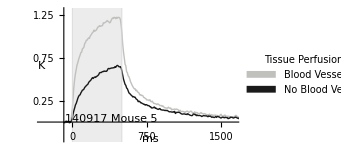

```mathematica
grSDBloodVar=Show[
Show[meanPlot[#[[1]],#[[2]],{-11,620-11}*samplingRate]& /@ Transpose[{gagFitDataBloodVar,gagColors}],ImageSize->72*3.5,
GridLines->{{0,500},None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-40,210}*samplingRate,{-0.2,1.3}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,1500,250}],{0.25,0.5,0.75,1,1.25}},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-11*samplingRate,0},LabelStyle->{FontSize->9,FontWeight->"Bold"},
Prolog->{Opacity[0.15,Gray], Rectangle[{0,-1},{500,7}]},
Epilog->{Text["ms",{101*samplingRate,-0.2},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-40*samplingRate,0.65},BaseStyle->{FontSize->9,FontWeight->"Bold"}],
Inset[gagLegend,{145*samplingRate,0.75}],Text["140917 Mouse 5",{50*samplingRate,0.04},BaseStyle->{FontSize->2}]}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.AverageBloodVar.png",grSDBloodVar,ImageResolution->600]
```

140917.AverageBloodVar.png

```mathematica
Export["140917.AverageBloodVar.pdf",grSDBloodVar,ImageResolution->600]
```

140917.AverageBloodVar.pdf

```mathematica
gagMeanDataBloodVar= Mean/@gagFitDataBloodVar;
```

```mathematica
Dimensions[gagMeanDataBloodVar]
```

{2,620}

```mathematica
gagMaxDataBloodVar=Max/@gagMeanDataBloodVar
```

{1.21922,0.659444}

```mathematica
gagMaxDataBloodVar=Map[ToString[NumberForm[#,{3,2}],OutputForm]&,gagMaxDataBloodVar,{1}]
```

{1.22,0.66}

```mathematica
gagMaxDataBloodVar=ToExpression[gagMaxDataBloodVar]
```

{1.22,0.66}

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

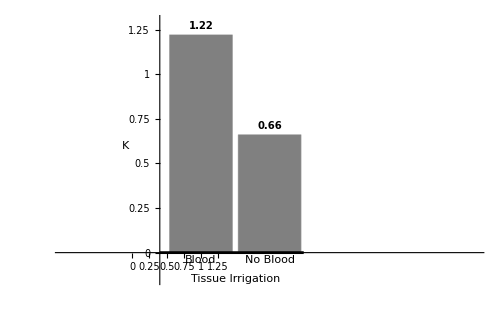

```mathematica
gagMaxTempGraph=BarChart[gagMaxDataBloodVar,
PlotRange->{{-1,5},{-0.15,1.3}},
ChartLabels->{{"Blood","No Blood"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{{0,0.25,0.5,0.75,1,1.25}},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Tissue Irrigation",{1.5,-0.15},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Text["K",{-0.1,0.6},BaseStyle->{FontSize->12,FontWeight->"Bold"}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.BloodVarMaxTemp.png",gagMaxTempGraph]
```

140917.BloodVarMaxTemp.png

```mathematica
Export["140917.BloodVarMaxTemp.pdf",gagMaxTempGraph]
```

140917.BloodVarMaxTemp.pdf

## Change data to {{time,value}, ....} format and Fit Functions

```mathematica
gagMakeTrialXY[data_, startPoint_Integer, endPoint_Integer]:=Module[{gagTimecourseR},
gagTimecourseR =Range[0, endPoint-startPoint ] *samplingRate;
Flatten[ 
Transpose[{gagTimecourseR,#[[startPoint;;endPoint]]}]&  /@ data,   1
]
];
```

```mathematica
gagModelModelRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc, tempShift},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{0.4*a*Log[0.01*c* x+0.1*b]},
{a,b,c},x]]] 
];
```

```mathematica
gagModelShiftFactorRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc,tempShift},
tempFunc=gagModelFuncRLog[data, startPoint, endPoint];
tempShift= x /. Flatten[Solve[ Evaluate[tempFunc[x]]==0, x]];
tempShift
];
```

```mathematica
gagModelFuncRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelRLog[data, startPoint, endPoint]["BestFit"];
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
gagModelModelFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{a*ⅇ^(b*(x+7)) +aa*ⅇ^(b*bb*(x+90)),{0 < a<5,-0.5<b<-0.0001 ,0<aa<5,0<bb<1}},
{a,c,b,aa,bb,cc},x]]]
];
```

```mathematica
gagModelFuncFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelFExp[data, startPoint, endPoint]["BestFit"] ;
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
Manipulate[
Show[grSDBloodVar,Plot[a*ⅇ^(b*(x)) +aa*ⅇ^(bb*(x)),{x,fallStart,trialLength},PlotRange->All],
PlotRange->All],
{{a,230.},0,1500},{{b,-0.0612},-0.2,0.2},{{aa,0.31},0,5},{{bb,0.0075},-1,0.3}
];
```

## Fit Function BootStrap

```mathematica
gagBootStrapData=Table[RandomSample[#,10],{500}]& /@gagFitDataBloodVar;
Dimensions[gagBootStrapData]
```

{2,500,10,620}

```mathematica
gagBootStrapModel= ParallelMap[gagModelModelRLog[#,stimStart, stimEnd]&, gagBootStrapData[[#]]]& /@Range[2];
Dimensions[gagBootStrapModel]
```

{2,500}

```mathematica
gagBootStrapModelParams=#["BestFitParameters"]&/@gagBootStrapModel[[#]]&/@Table[x,{x,1,2,1}];
Dimensions[gagBootStrapModelParams]
```

{2,500,3}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{2,3,500}

```mathematica
gagBootStrapModelParams={a/.#& /@gagBootStrapModelParams[[;;,1,#]]*0.4&/@Table[x,{x,1,500,1}],b/.#& /@gagBootStrapModelParams[[;;,2,#]]*0.1&/@Table[x,{x,1,500,1}],c/.#& /@gagBootStrapModelParams[[;;,3,#]]*0.01&/@Table[x,{x,1,500,1}]};
Dimensions[gagBootStrapModelParams]
```

{3,500,2}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{3,2,500}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{2,1,3}];
Dimensions[gagBootStrapModelParams]
```

{2,3,500}

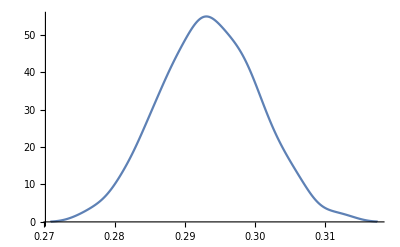
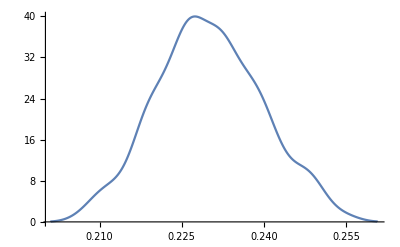
5
6[{{-Graphics-,0.99976},{-Graphics-,0.326448}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,1]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,2,1}]//TableForm[{5,6}]
```

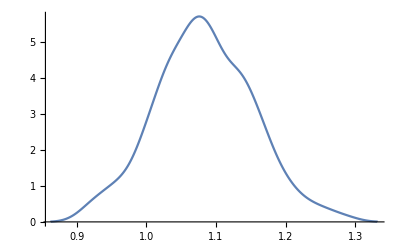
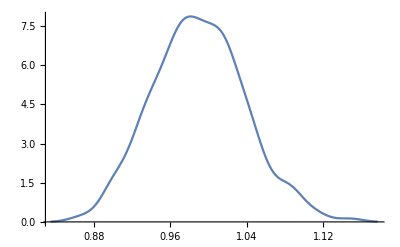
5
6[{{-Graphics-,0.99976},{-Graphics-,0.326448}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,2]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,2,1}]//TableForm[{5,6}]
```

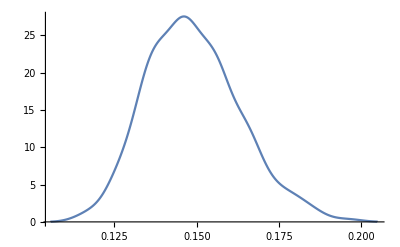
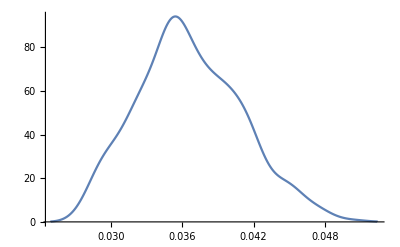
5
6[{{-Graphics-,0.99976},{-Graphics-,0.326448}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,3]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,2,1}]//TableForm[{5,6}]
```

```mathematica
gagBootStrapModelParamsMedian=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[2]];
Dimensions[gagBootStrapModelParamsMedian]
```

{3,2}

```mathematica
gagBootStrapModelParams99= Transpose[Quantile[#,{0.01,0.99},{{1/2,0},{0,1}}]&/@gagBootStrapModelParams[[#]]&/@Range[2],{2,1,3}];
Dimensions[gagBootStrapModelParams99]
```

{3,2,2}

```mathematica
gagBootStrapModelParamsMedian0=gagBootStrapModelParamsMedian;
```

```mathematica
gagBootStrapModelParamsMedian0={Range[2],#}&/@gagBootStrapModelParamsMedian0;
Dimensions[gagBootStrapModelParamsMedian0]
```

{3,2,2}

```mathematica
gagBootStrapModelParamsMedian0=Transpose[gagBootStrapModelParamsMedian0,{1,3,2}];
```

```mathematica
gagBootStrapModelParamsMedian0
```

{{{1,0.293296},{2,0.230026}},{{1,1.08073},{2,0.98815}},{{1,0.147891},{2,0.0361942}}}

```mathematica
gagBootStrapModelParamsMedian1=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[2]]
```

{{0.293296,0.230026},{1.08073,0.98815},{0.147891,0.0361942}}

```mathematica
gagBootStrapModelParamsMedian1=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParamsMedian1
```

{{0.29, 0.23},{1.08, 0.99},{0.15, 0.04}}

```mathematica
gagBootStrapModelParamsMedian1=ToExpression[gagBootStrapModelParamsMedian1]
```

{{0.29,0.23},{1.08,0.99},{0.15,0.04}}

```mathematica
gagBootStrapModelParams991=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParams99
```

{{{0.28, 0.31}, {0.21, 0.25}},{{0.92, 1.26}, {0.89, 1.11}},{{0.12, 0.19}, {0.03, 0.05}}}

```mathematica
gagBootStrapModelParams991=ToExpression[gagBootStrapModelParams991]
```

{{{0.28,0.31},{0.21,0.25}},{{0.92,1.26},{0.89,1.11}},{{0.12,0.19},{0.03,0.05}}}

```mathematica
gagBootStrapModelParams991=gagBootStrapModelParams991-gagBootStrapModelParamsMedian1
```

{{{-0.01,0.02},{-0.02,0.02}},{{-0.16,0.18},{-0.1,0.12}},{{-0.03,0.04},{-0.01,0.01}}}

```mathematica
gagCValueBootStrapData=Table[gagBootStrapModelParamsMedian1[[i,j]]->gagBootStrapModelParams991[[i,j]],{i,1,Length[gagBootStrapModelParamsMedian1]},{j,1,Length[gagBootStrapModelParamsMedian1[[1]]]}]
```

{{0.29→{-0.01,0.02},0.23→{-0.02,0.02}},{1.08→{-0.16,0.18},0.99→{-0.1,0.12}},{0.15→{-0.03,0.04},0.04→{-0.01,0.01}}}

```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{errorN,errorP},{errorN=Flatten[meta],errorP=Flatten[meta]};
{errorN,errorP}=If[{errorN,errorP}==={},0,Last[{errorN,errorP}]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Thickness[0.0035],Line[{{{(x0+x1)/2,y1+errorN},{(x0+x1)/2,y1+errorP}},{{1/4 (3 x0+x1),y1+errorP},{1/4 (x0+3 x1),y1+errorP}},{{1/4 (3 x0+x1),y1+errorN},{1/4 (x0+3 x1),y1+errorN}}}]}}]
```

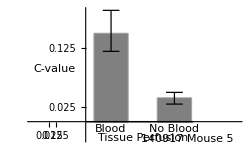

```mathematica
gagCValueBootStrapGraph=BarChart[gagCValueBootStrapData[[3]],ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-0.25,3},{-0.03,0.19}},
ChartLabels->{{"Blood","No Blood"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->0.9,ChartBaseStyle->EdgeForm[Thickness[0.00597]],
AspectRatio->1/GoldenRatio,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->9],Directive[Black,Thickness[0.004],FontSize->9]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.6,0},
Ticks->{Table[n,{n,0.025,0.175,0.05}]},TicksStyle->Directive[Black,9],ChartStyle->Gray,TicksStyle->Bold,
LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["Tissue Perfusion",{1.5,-0.028},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["C-value",{0.1,0.09},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["140917 Mouse 5",{2.2,-0.03},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.BloodVarC-ValueBootStrap.png",gagCValueBootStrapGraph,ImageResolution->600]
```

140917.BloodVarC-ValueBootStrap.png

```mathematica
Export["140917.BloodVarC-ValueBootStrap.pdf",gagCValueBootStrapGraph,ImageResolution->600]
```

140917.BloodVarC-ValueBootStrap.pdf

```mathematica
gagBootStrapModelParamsMedian={gagBootStrapModelParamsMedian,gagBootStrapModelParams99};
```

```mathematica
Dimensions[gagBootStrapModelParamsMedian]
```

{2,3,2}

```mathematica
gagBootStrapModelParamsMedian=Transpose[gagBootStrapModelParamsMedian,{3,1,2}]
Dimensions[gagBootStrapModelParamsMedian]
```

{{{0.293296,{0.277369,0.310464}},{0.230026,{0.20905,0.251828}}},{{1.08073,{0.920914,1.26233}},{0.98815,{0.893362,1.11002}}},{{0.147891,{0.118636,0.185722}},{0.0361942,{0.0282293,0.0474543}}}}

{3,2,2}

```mathematica
gagBootStrapModelParamsMedian=Map[(ToString[NumberForm[#[[1]],{3,2}]] <> " ("<>ToString[NumberForm[#[[2,1]],{3,2}]]<>"-"<>ToString[NumberForm[#[[2,2]],{3,2}]]<>")" )&, gagBootStrapModelParamsMedian,{2}]
```

{{0.29 (0.28-0.31),0.23 (0.21-0.25)},{1.08 (0.92-1.26),0.99 (0.89-1.11)},{0.15 (0.12-0.19),0.04 (0.03-0.05)}}

```mathematica
gagBootStrapModelParamsMedian=Prepend[gagBootStrapModelParamsMedian,{"Tissue Perfusion","Blood Vessel","No Blood Vessel"}];
Dimensions[gagBootStrapModelParamsMedian]
```

{4}

```mathematica
gagBootStrapModelParamsMedian[[2]]
```

{0.29 (0.28-0.31),0.23 (0.21-0.25)}

```mathematica
gagBootStrapModelParamsMedian[[2]]= Prepend[gagBootStrapModelParamsMedian[[2]],"a (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[3]]= Prepend[gagBootStrapModelParamsMedian[[3]],"b (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[4]]= Prepend[gagBootStrapModelParamsMedian[[4]],"c (1%CI-99%CI)"];
```

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
gagBootStrapModelParamsMedian//InputForm
```

{{"Tissue Perfusion", "Blood Vessel", "No Blood Vessel"}, {"a (1%CI-99%CI)", "0.29 (0.28-0.31)", "0.23 (0.21-0.25)"}, {"b (1%CI-99%CI)", "1.08 (0.92-1.26)", "0.99 (0.89-1.11)"}, 
 {"c (1%CI-99%CI)", "0.15 (0.12-0.19)", "0.04 (0.03-0.05)"}}

```mathematica
gagParamsTableBootStrap=Grid[gagBootStrapModelParamsMedian,Frame->All,ItemSize->{{1->9,2;;12->8},1.5},BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}},Background->{None,{4->Opacity[0.35,Gray]}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Tissue Perfusion | Blood Vessel | No Blood Vessel
a (1%CI-99%CI) | 0.29 (0.28-0.31) | 0.23 (0.21-0.25)
b (1%CI-99%CI) | 1.08 (0.92-1.26) | 0.99 (0.89-1.11)
c (1%CI-99%CI) | 0.15 (0.12-0.19) | 0.04 (0.03-0.05)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.ParamsTableBootStrap.png",gagParamsTableBootStrap,ImageResolution->600]
```

140917.ParamsTableBootStrap.png

```mathematica
Export["140917.ParamsTableBootStrap.pdf",gagParamsTableBootStrap,ImageResolution->600]
```

140917.ParamsTableBootStrap.pdf

## Fit Function

```mathematica
{funcR1,funcR2}=gagModelFuncRLog[#,stimStart, stimEnd]& /@gagFitDataBloodVar
```

{0.293838 Log[1.07965+0.147557 #1]&,0.229161 Log[0.989255+0.0366039 #1]&}

```mathematica
{modelR1,modelR2}=gagModelModelRLog[#,stimStart, stimEnd]& /@gagFitDataBloodVar;
```

```mathematica
gagModelParams={modelR1["BestFitParameters"],modelR2["BestFitParameters"]};
```

```mathematica
gagModelParams=Transpose[gagModelParams]
```

{{a→0.734594,a→0.572903},{b→10.7965,b→9.89255},{c→14.7557,c→3.66039}}

```mathematica
gagModelParams={a/.#& /@gagModelParams[[1]]*0.4,b/.#& /@gagModelParams[[2]]*0.1,c/.#& /@gagModelParams[[3]]*0.01}
```

{{0.293838,0.229161},{1.07965,0.989255},{0.147557,0.0366039}}

```mathematica
gagModelParams0=Transpose[{{0.75,1.25},#}]&/@gagModelParams
```

{{{0.75,0.293838},{1.25,0.229161}},{{0.75,1.07965},{1.25,0.989255}},{{0.75,0.147557},{1.25,0.0366039}}}

```mathematica
gagModelParams=Map[ToString[NumberForm[#,{4,3}]]&,gagModelParams,{2}]
```

{{0.294,0.229},{1.080,0.989},{0.148,0.037}}

```mathematica
gagModelParams1=ToExpression[gagModelParams]
```

{{0.294,0.229},{1.08,0.989},{0.148,0.037}}

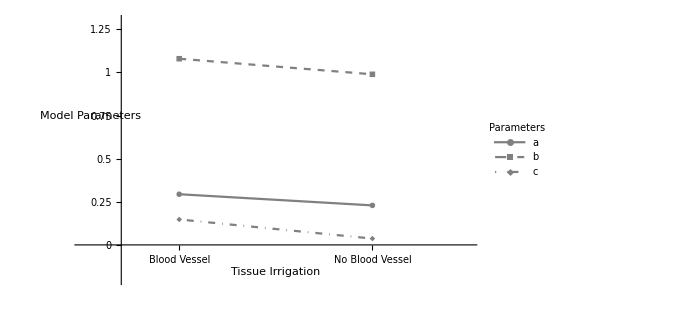

```mathematica
gagAvalueGraph=ListLinePlot[
gagModelParams0, 
PlotRange->{{0.5,1.5},{-0.2,1.3}},AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.6,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{0.9,0.55},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{0.75,"Blood Vessel"},{1.25,"No Blood Vessel"}},{0,0.25,0.5,0.75,1,1.25}},Epilog->{Text["Tissue Irrigation",{1,-0.16},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.52,0.75},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.C-valueBloodVar.png",gagAvalueGraph]
```

140917.C-valueBloodVar.png

```mathematica
Export["140917.C-valueBloodVar.pdf",gagAvalueGraph]
```

140917.C-valueBloodVar.pdf

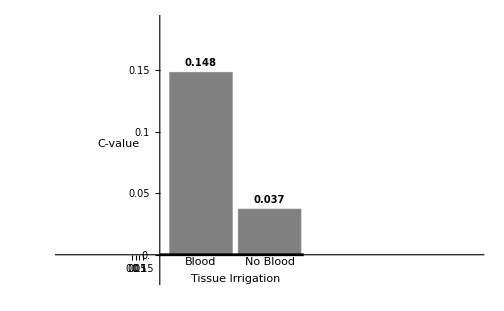

```mathematica
gagCValueGraph=BarChart[gagModelParams1[[3]],
PlotRange->{{-1,5},{-0.02,0.19}},
ChartLabels->{{"Blood","No Blood"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.175,0.025}]},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Tissue Irrigation",{1.5,-0.02},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["C-value",{-0.2,0.09},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.BloodVarC-Value.png",gagCValueGraph]
```

140917.BloodVarC-Value.png

```mathematica
Export["140917.BloodVarC-Value.pdf",gagCValueGraph]
```

140917.BloodVarC-Value.pdf

```mathematica
gagModelParams=Prepend[gagModelParams,{"Tissue irrigation","Blood Vessel","No Blood Vessel"}];
```

```mathematica
gagModelParams[[4]]
```

{0.148,0.037}

```mathematica
gagModelParams[[2]]= Prepend[gagModelParams[[2]],"a"];
```

```mathematica
gagModelParams[[3]]= Prepend[gagModelParams[[3]],"b"];
```

```mathematica
gagModelParams[[4]]= Prepend[gagModelParams[[4]],"c"];
```

```mathematica
gagModelParams//InputForm
```

{{"Tissue irrigation", "Blood Vessel", "No Blood Vessel"}, {"a", "0.294", "0.229"}, {"b", "1.080", "0.989"}, {"c", "0.148", "0.037"}}

```mathematica
gagParamsTable=Grid[gagModelParams,Frame->All,ItemSize->{Automatic,2},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Tissue irrigation | Blood Vessel | No Blood Vessel
a | 0.294 | 0.229
b | 1.080 | 0.989
c | 0.148 | 0.037

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.ParamsTableBloodVar.png",gagParamsTable]
```

140917.ParamsTableBloodVar.png

```mathematica
Export["140917.ParamsTableBloodVar.pdf",gagParamsTable]
```

140917.ParamsTableBloodVar.pdf

```mathematica
{shiftR1,shiftR2}=gagModelShiftFactorRLog[#,stimStart, stimEnd]& /@gagFitDataBloodVar
```

{-0.539766,0.293536}

```mathematica
grRPlot=Plot[{funcR1[x+shiftR1*samplingRate],funcR2[x+shiftR2*samplingRate]},{x,0,(stimEnd+2)*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

```mathematica
{funcF1,funcF2}=gagModelFuncFExp[#,fallStart, trialLength]& /@gagFitDataBloodVar
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.03173×10^-12, 0.0000175315, 8.45871×10^-13}, is returned.

{0.925895 ⅇ^(-0.0161455 (7+#1))+0.410528 ⅇ^(-0.00149795 (90+#1))&,0.417137 ⅇ^(-0.0133955 (7+#1))+0.311202 ⅇ^(-0.00153997 (90+#1))&}

```mathematica
grFPlot=Plot[{funcF1[x-(fallStart-stimStart)*samplingRate],funcF2[x-(fallStart-stimStart)*samplingRate]},{x,(fallStart-stimStart)*samplingRate,trialLength*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

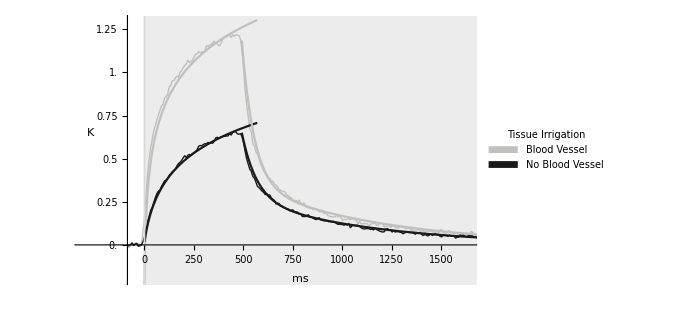

```mathematica
Show[grSDBloodVar,grRPlot,grFPlot]
```